## Derive analytical solution for no-extensional stress case

```mathematica
eqsimple = b y[x] y'[x] == a *y[x]-1
bc1 = {y[1]==0};
sol=DSolve[{eqsimple,bc1},y[x],x];
ysol = y[x]/.sol[[1]]
sinθ = 0.1;(*sinθ*)
alpha = 1;(*ρgh/τ0 - this is the ratio of gravity to friction*)
ymax = Evaluate[ysol/.{a->alpha*sinθ,b->alpha*Sqrt[1-sinθ^2],x->0}]
```

b y[x] y'[x]==-1+a y[x]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(1+ProductLog[-ⅇ^(-1-a^2/b+(a^2 x)/b)])/a

1.35158

## Compute numerical solution for case with extensional stresses

-a y[x]+b y[x] y'[x]+y'[x]^2+y[x] y''[x]==1

-a y[x]+b y[x] y'[x]+y'[x]^2+y[x] y''[x]==-1

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

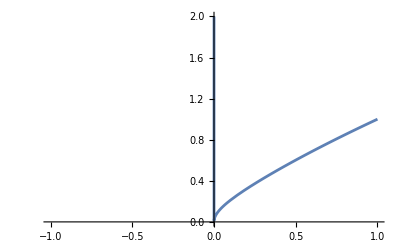

```mathematica
(*Define the differential equation*)
eqn=y[x] y''[x]+b y[x] y'[x]+(y'[x])^2 - a *y[x]==1
(*Define boundary conditions*)
bcs={y[0]==0.01,y[1]==1};
numSol=NDSolve[{eqn/. {a->alpha*sinθ,b->alpha*Sqrt[1-sinθ^2]},bcs},y[x],{x,0,1}];

eqn=y[x] y''[x]+b y[x] y'[x]+(y'[x])^2 - a *y[x]==-1
bcs={y[0]==0.5,y[1]==1};
numSol2=NDSolve[{eqn/. {a->alpha*sinθ,b->alpha*Sqrt[1-sinθ^2]},bcs},y[x],{x,0,1}];
Plot[Evaluate[y[x]/. numSol],{x,-1,1},PlotRange->{0,2}]
```

## Plot comparison of both cases for a given set of parameters

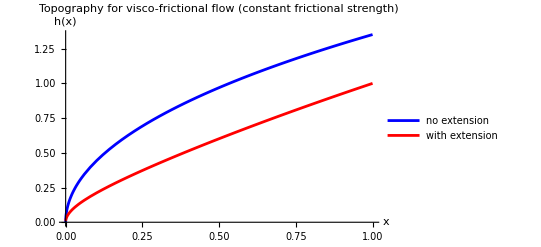

```mathematica
Plot[{Evaluate[(ysol)/.{a->alpha*sinθ,b->alpha*Sqrt[1-sinθ^2],x->1-x}],Evaluate[y[x]/. numSol]},{x,0,1},PlotLabel->"Topography for visco-frictional flow (constant frictional strength)",AxesLabel->{"x","h(x)"},PlotStyle->{Blue,Red},PlotLegends->{"no extension","with extension"}]
```

Plot results for varying a-values for analytical solution (no extensional stresses)

```mathematica
(*aValues={0.1,0.2,0.3,0.4,0.5};
alpha = 0.3;

(*Plot ySol for different'a' values,keeping b fixed*)
Plot[Evaluate[Table[ysol/. {a->alpha*aVal,b->alpha*Sqrt[1-aVal^2]},{aVal,aValues}]],{x,0,1},PlotLabel->"Solutions for Different Values of a",AxesLabel->{"x","y"},PlotStyle->ColorData[97]/@Range[5],PlotLegends->Placed[LineLegend[aValues,LegendLabel->"a Values"],{0.8,0.8}]]*)
```

```mathematica
eqnMC=y[x] y''[x]-a/2  y'[x]+2*(y'[x])^2 ==0.5-a/2
(*Define boundary conditions*)
bcs={y[0]==0.01,y[1]==1};
numSol=NDSolve[{eqnMC/. {a->1},bcs},y[x],{x,0,1}];
```

-1/2 a y'[x]+2 y'[x]^2+y[x] y''[x]==0.5-a/2

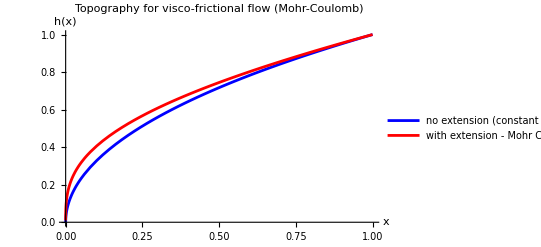

```mathematica
Plot[{Evaluate[(ysol/ymax)/.{a->alpha*sinθ,b->alpha*Sqrt[1-sinθ^2],x->1-x}],Evaluate[y[x]/. numSol]},{x,0,1},PlotLabel->"Topography for visco-frictional flow (Mohr-Coulomb)",AxesLabel->{"x","h(x)"},PlotStyle->{Blue,Red},PlotLegends->{"no extension (constant τb)","with extension - Mohr Coulomb"}]
```